```mathematica
Subscript[w, ϵ_][y_]:=1/2(1 - Tanh[y/(4 ϵ)]);
Subscript[u, ϵ_][x_,t_]:=Subscript[w, ϵ][x - 1/2 t];
```

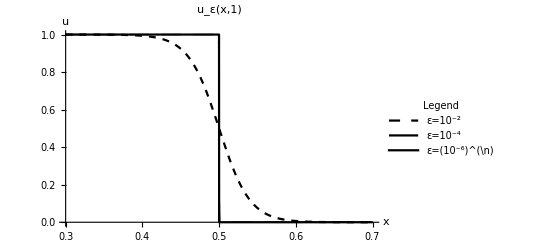

```mathematica
Plot[{Subscript[u, 10^-2][x,1],Subscript[u, 10^-4][x,1],Subscript[u, 10^-6][x,1]},{x,.3,.7},AxesLabel->{Style["x",FontSize->14],Style["u",FontSize->14]},AxesStyle->Directive[FontSize->12],PlotLabel->Style["u_ε(x,1)",FontSize->16],PlotLegends->Placed[LineLegend[{"ε=10^-2","ε=10^-4","ε=(10^-6)^(\n)"},LegendLabel->"Legend",LabelStyle->Directive[FontSize->12]],{.88,.8}],PlotStyle->{Directive[Dashed,Black],Directive[Dashing[{Large,Medium}],Black,Thick],Directive[Black]}]
```